```mathematica
R1=10000;
R2=10000;
R3=10000;
C2=10*10^-9;
```

```mathematica
L1=10*10^-3;
```

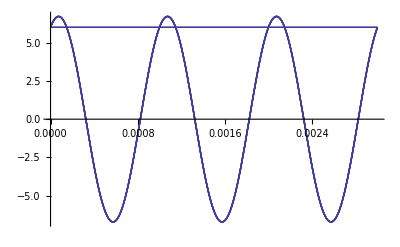

```mathematica
uZ=3+6ⅉ;

uzel1=iUf==iLf+iR1f;
uzel2=iR1f+iLf==iR2f+iR3f;
uzel3=iR2f==iC2f;
rovR1=u1f-u2f==R1*iR1f;
rovR2=u2f-u3f==R2*iR2f;
rovR3=u2f==R3*iR3f;
rovL=u1f-u2f==L*ⅉ*ω*iLf;
rovC2=iC2f==C2*ⅉ*ω*u2f;
rovU=u1f==uZ;
rovnice={uzel1,uzel2,uzel3,rovC2,rovR1,rovR2,rovR3,rovU,rovL};
vysledek=Solve[rovnice];

Plot[{Im[u1f*ⅇ^(ⅉ*ω*t)/.vysledek/.ω->1000*2*π]},{t,0,0.003}]
```